```mathematica
α=0.005
```

0.005

```mathematica
Ω=2
```

2

```mathematica
β=10
```

10

```mathematica
Subscript[ω, c]=1000
```

1000

```mathematica
ω'=√5
```

√5

```mathematica
f1[k_]=α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k-(Ω+ω'))
```

(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(-2-√5+k)

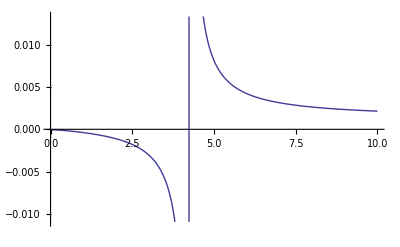

```mathematica
Plot[f1[k],{k,0,10}]
```

```mathematica
i1 = NIntegrate[f1[k],{k,3*(Ω+ω')/2,∞}]
```

1.27152

```mathematica
i2 = NIntegrate[f1[k],{k,0,(Ω+ω')/2}]
```

-0.00103127

```mathematica
i3 = NIntegrate[f1[k],{k,(Ω+ω')/2,(Ω+ω')-0.00001}]
```

-0.0620334

```mathematica
i4 = NIntegrate[f1[k],{k,(Ω+ω')+0.00001,3*(Ω+ω')/2}]
```

0.0672837

```mathematica
Subscript[i, tot]=i1+i2+i3+i4
```

1.27573

```mathematica
f2[k_]=-α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k-(ω'-Ω))
```

-(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(2-√5+k)

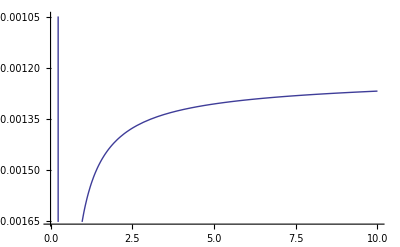

```mathematica
Plot[f2[k],{k,0,10}]
```

```mathematica
Subscript[l, 1]=NIntegrate[f2[k],{k,3*(ω'-Ω)/2,∞}]
```

-1.25207

```mathematica
Subscript[l, 2]=NIntegrate[f2[k],{k,0,(ω'-Ω)/2}]
```

0.000181072

```mathematica
Subscript[l, 3]=NIntegrate[f2[k],{k,(ω'-Ω)/2,(ω'-Ω)-10^-4}]
```

0.00243314

```mathematica
Subscript[l, 4]=NIntegrate[f2[k],{k,(ω'-Ω)+10^-4,3*(ω'-Ω)/2}]
```

-0.00262725

```mathematica
Subscript[l, tot]=Subscript[l, 1]+Subscript[l, 2]+Subscript[l, 3]+Subscript[l, 4]
```

-1.25209

```mathematica
f3[k_]=-α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k+ω'+Ω)
```

-(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(2+√5+k)

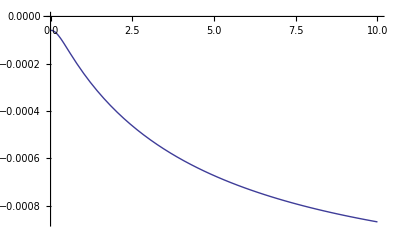

```mathematica
Plot[f3[k],{k,0,10}]
```

```mathematica
NIntegrate[f3[k],{k,0,∞}]
```

-1.224

```mathematica
f4[k_]=α/4*k*Exp[-k/Subscript[ω, c]]*Coth[β*k/2]/(k+ω'-Ω)
```

(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(-2+√5+k)

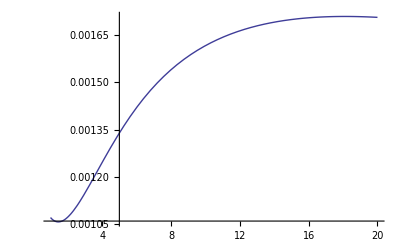

```mathematica
Plot[(0.0025 ⅇ^(-k/100) k Coth[k/2])/(4+k),{k,1,20}]
```

```mathematica
NIntegrate[f4[k],{k,0,∞}]
```

1.24782

```mathematica
Regsc=Subscript[i, tot]+Subscript[l, tot]+NIntegrate[f3[k],{k,0,∞}]+NIntegrate[f4[k],{k,0,∞}]
```

0.0474728

```mathematica
f[k_]=f1[k]+f2[k]+f3[k]+f4[k]
```

(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(-2-√5+k)-(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(2-√5+k)+(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(-2+√5+k)-(0.00125 ⅇ^(-k/1000) k Coth[5 k])/(2+√5+k)

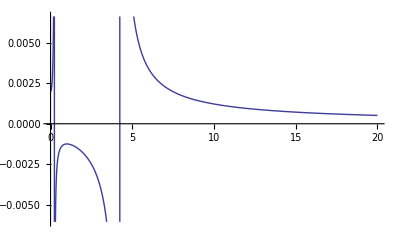

```mathematica
Plot[f[k],{k,0,20}]
```

```mathematica
Regcs=NIntegrate[f3[k],{k,0,∞}]-Subscript[l, tot]-NIntegrate[f4[k],{k,0,∞}]+Subscript[i, tot]
```

0.0559957